Exercises for Section 14 | Coordinates and Graphics

Make graphics of 5 concentric circles centered at {0,0} with radii 1, 2, ... , 5. |

EXPECTED OUTPUT »

-Graphics- | ×

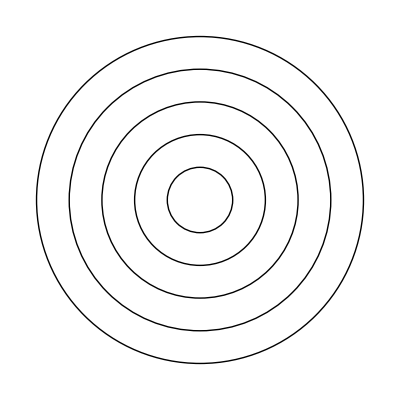

```mathematica
Graphics[Table[Circle[{0,0},r],{r,1,5,1}]]
```

Make 10 concentric circles with random colors. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

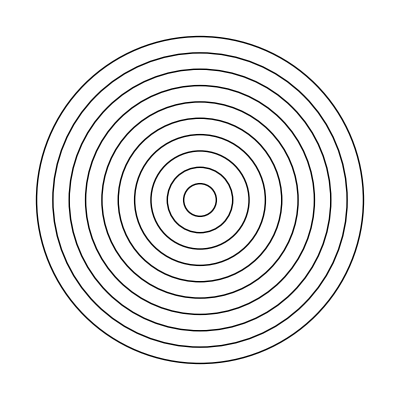

```mathematica
Graphics[Table[Style[Circle[{0,0},r],RandomColor[]],{r,1,10,1}]]
```

Make graphics of a 10×10 grid of circles with radius 1 centered at integer points {x,y}. |

EXPECTED OUTPUT »

-Graphics- | ×

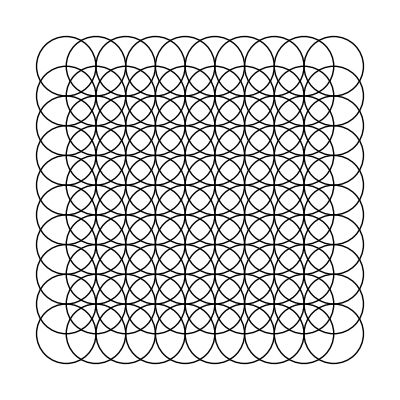

```mathematica
Graphics[Table[Circle[{x,y},1],{x,10},{y,10}]]
```

Make a 10×10 grid of points with coordinates at integer positions up to 10. |

EXPECTED OUTPUT »

-Graphics- | ×

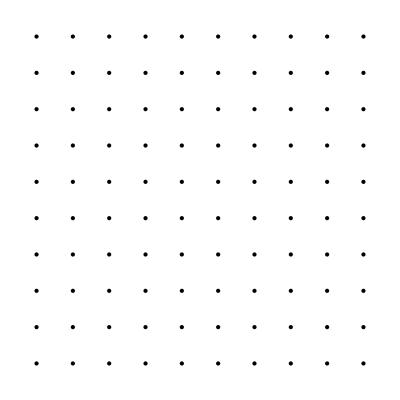

```mathematica
Graphics[Table[Point[{x,y}],{x,10},{y,10}]]
```

Make a Manipulate with between 1 and 20 concentric circles. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{n}]],{n,1,20,1}];
Manipulate[Graphics[Table[Circle[{0,0},r],{r,1,10,1}]],{}];
Manipulate[Graphics[Table[Circle[{0,0},r],1]],{r,1,10,1}];
Manipulate[Graphics[Table[Table[Circle[{0,0},r],{r,1,20,1}],n]],{n,1,20,1}];
Manipulate[Graphics[Table[Circle[{0,0}, r], {r, n}]], {n, 1, 20, 1}]
```

Manipulate::vsform: Manipulate argument {} does not have the correct form for a variable specification.

```mathematica
Manipulate[Graphics[Table[Circle[{0,0},r],{r,n}]],{n,1,20,1}]
```

Place 50 spheres with random colors at random integer coordinates up to 10. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics3D[Table[{RandomColor[],Sphere[RandomInteger[10,3]]},50]]
```

-Graphics3D-

Make a 10×10×10 array of spheres with RGB components ranging from 0 to 1. The spheres should be centered at integer coordinates, and should just touch each other. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics3D[Table[{RGBColor[x/10,y/10,z/10],Sphere[{x,y,z},1/2]},{x,10},{y,10},{z,10}]]
```

-Graphics3D-

Make a Manipulate with t varying between −2 and +2 that contains circles of radius x centered at {t*x,0} with x going from 1 to 10. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[Graphics[Table[Circle[{t*x,0},x],{x,1,10,1}]],{t,-2,2}]
```

Make a 5×5 array of regular hexagons with size 1/2, centered at integer points. |

EXPECTED OUTPUT »

-Graphics- | ×

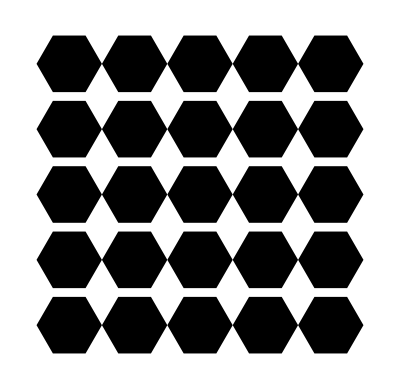

```mathematica
Graphics[Table[RegularPolygon[{x,y},0.5,6],{x,5},{y,5}]]
```

Make a line in 3D that goes through 50 random points with integer coordinates randomly chosen up to 50. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics3D[Line[Table[RandomInteger[50,3],50]]]
```

-Graphics3D-

Make a Manipulate to create an n×n regular grid of points at integer positions, with n going from 5 to 20. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Manipulate[Graphics[Table[Point[{x,y}],{x,n},{y,n}]],{n,5,20,1}]
```

Place 30 radius-1 circles with random colors at random integer coordinates up to 10. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

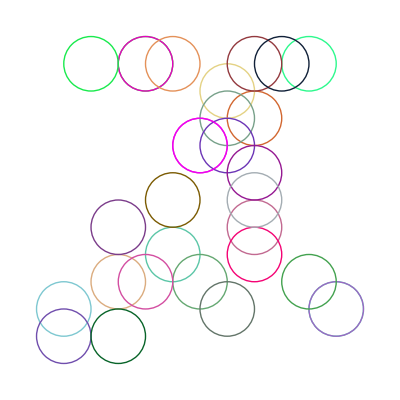

```mathematica
Graphics[Table[{RandomColor[],Circle[RandomInteger[10,2],1]},30]]
```

Display 100 polygons with side length 10, opacity .5, and random choices of colors, sides between 3 and 8, and integer coordinates up to 100. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

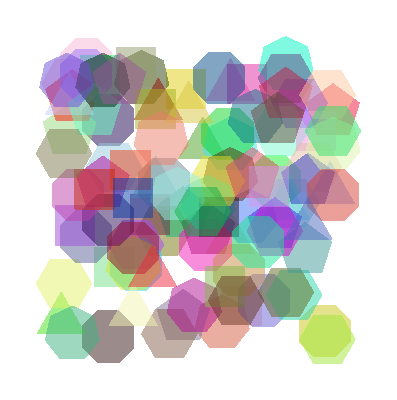

```mathematica
Graphics[Table[{RandomColor[], Opacity[0.5], 
   RegularPolygon[{RandomInteger[100], RandomInteger[100]}, 10, 
    RandomInteger[{3, 8}]]}, 100]]
```

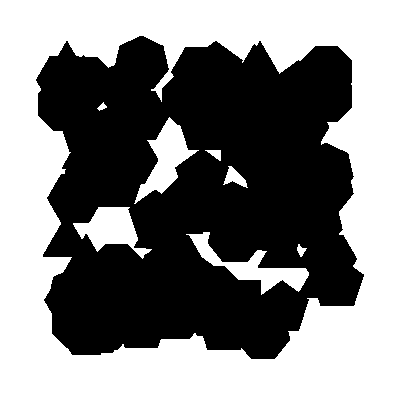

```mathematica
Graphics[Table[
  Style[RegularPolygon[{RandomInteger[100], RandomInteger[100]}, 10, 
    RandomInteger[{3, 8}]], Opacity[0.5], RandomColor[]], 100]]
    "Works with style, not directives";
```

Make a 10×10×10 array of points in 3D, with each point having a random color. |

SAMPLE EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics3D[Table[Style[Point[{x,y,z}],RandomColor[]],{x,10},{y,10},{z,10}]]
```

-Graphics3D-

Take the first two digits of numbers from 10 to 100 and draw a line that uses them as coordinates. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics[Line[Table[Take[IntegerDigits[n],2],{n,10,100}]]]
```

-Graphics-

Take the first 3 digits of numbers from 100 to 1000 and draw a line in 3D that uses them as coordinates. |

EXPECTED OUTPUT »

-Graphics- | ×

```mathematica
Graphics3D[Line[Table[Take[IntegerDigits[n],3],{n,100,1000}]]]
```

-Graphics3D-